15.9444

{μ→16.007}

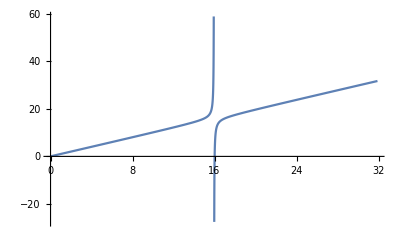

```mathematica
σ=0.1;
S=10;
T=1;
K=50;
r=0.02;

Dcond = (Log[K/S]-(r-σ^2/2)T)/σ

f[μ_]:=μ-S σ Exp[(r-σ^2/2)T+σ μ]/(S  Exp[(r-σ^2/2)T+σ  μ]-K)
FindRoot[f[μ]==0,{μ,1.1*Dcond,Dcond+0.0001,2Dcond}]
Plot[f[μ],{μ, 0, 2*Dcond}]
```